```mathematica
Solve[p^2+q^2+2*p*q*z+usq==0,{p}]//Simplify
```

{{p→-q z-√(-usq+q^2 (-1+z^2))},{p→-q z+√(-usq+q^2 (-1+z^2))}}

```mathematica
pplus[l_,z_,usq_]:=-l*z+√(-usq+l^2*(z^2-1));
pminus[l_,z_,usq_]:=-l*z-√(-usq+l^2*(z^2-1));
```

```mathematica
Γsmc[t_,Λ_,ω_,V0_]:=t+I*V0*(1-ⅇ^(-t/ω))*(1-ⅇ^((t-Λ)/ω))
```

```mathematica
Plotsmc[Λ_,ω_,V0_]:=ComplexListPlot[Table[Γsmc[λ,Λ,ω,V0],{λ,Subdivide[0,Λ,50]}]]
```

```mathematica
Table[pplus[0.1,z,-0.0016670826352479656],{z,-1,1,0.1}]
```

{0.14083,0.09+0.0152616 ⅈ,0.08+0.043965 ⅈ,0.07+0.0585911 ⅈ,0.06+0.0687962 ⅈ,0.05+0.0763735 ⅈ,0.04+0.0820544 ⅈ,0.03+0.0862144 ⅈ,0.02+0.0890669 ⅈ,0.01+0.0907354 ⅈ,0.+0.0912848 ⅈ,-0.01+0.0907354 ⅈ,-0.02+0.0890669 ⅈ,-0.03+0.0862144 ⅈ,-0.04+0.0820544 ⅈ,-0.05+0.0763735 ⅈ,-0.06+0.0687962 ⅈ,-0.07+0.0585911 ⅈ,-0.08+0.043965 ⅈ,-0.09+0.0152616 ⅈ,-0.0591701}

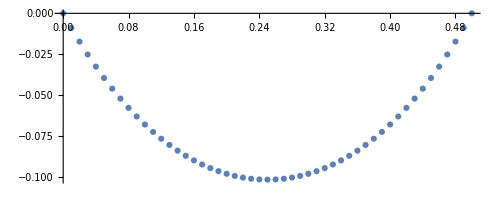

```mathematica
Plotsmc[0.5,0.2,-0.2]
```

```mathematica
PlotTarget[usq_,Λ_,ω_,V0_]:=Module[{lv,pltlv,plt1,plt2,zv=Subdivide[-1,1,50]},
lv=Table[Γsmc[λ,Λ,ω,V0],{λ,Subdivide[0,Λ,100]}];
pltlv=ComplexListPlot[lv,PlotStyle->Red,PlotRange->{{-0.1,1.1Λ},{V0,-V0}}];
plt1=ComplexListPlot[Flatten[Table[pplus[l,z,usq],{l,lv},{z,zv}]],PlotStyle->Blue];
plt2=ComplexListPlot[Flatten[Table[pminus[l,z,usq],{l,lv},{z,zv}]],PlotStyle->Brown];
Show[pltlv,plt1,plt2]
]
```

```mathematica
PlotTargetInc[usq_,Λ_,ω_,V0_]:=Module[{lv,pltlv,plt1,plt2,zv=Subdivide[-1,1,50]},
lv=Join[Subdivide[0.0,0.13,20],Table[Γsmc[λ,Λ,ω,V0],{λ,Subdivide[0,Λ,100]}]];
pltlv=ComplexListPlot[lv,PlotStyle->Red,PlotRange->{{-0.1,1.1Λ},{V0,-V0}}];
plt1=ComplexListPlot[Flatten[Table[pplus[l,z,usq],{l,lv},{z,zv}]],PlotStyle->Blue];
plt2=ComplexListPlot[Flatten[Table[pminus[l,z,usq],{l,lv},{z,zv}]],PlotStyle->Brown];
Show[pltlv,plt1,plt2]
]
```

```mathematica
Plotz[usq_,Λ_,ω_,V0_]:=Module[{lv,tmpf},
lv=Table[Γsmc[λ,Λ,ω,V0],{λ,Subdivide[0,Λ,200]}];
ComplexListPlot[Flatten[Table[(p^2+q^2+usq)/(2p*q+10^-50),{p,lv},{q,lv}]],PlotRange->{{-1.1,1.1},{-0.2,0.2}}]
]
```

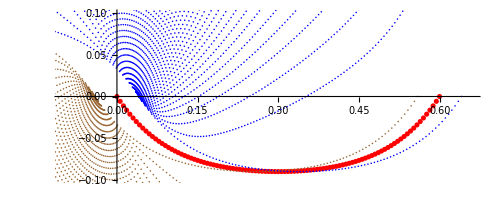

```mathematica
PlotTarget[-0.0016670826352479656,0.6,0.1,-0.1]
```

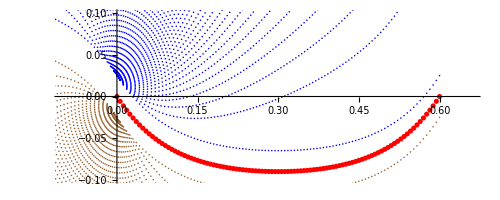

```mathematica
PlotTarget[0.0006318533591980965,0.6,0.1,-0.1]
```

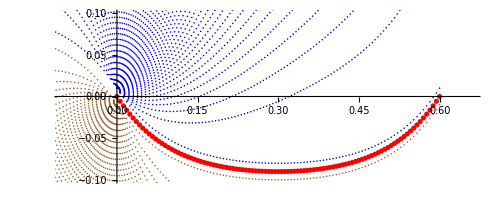

```mathematica
PlotTarget[0.0001,0.6,0.1,-0.1]
```

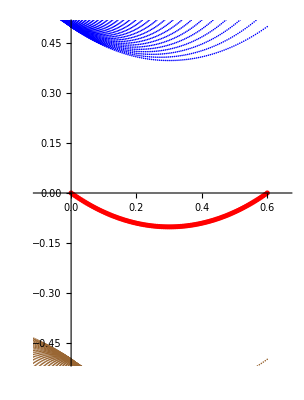

```mathematica
PlotTarget[0.5^2,0.6,0.5,-0.5]
```

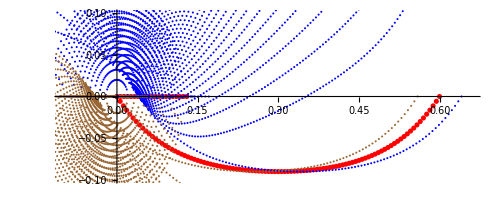

```mathematica
PlotTargetInc[-0.0016670826352479656,0.6,0.1,-0.1]
```

```mathematica
Plotz[-0.0016670826352479656,0.6,0.1,-0.2]
```

-Graphics-

```mathematica
Plotz[0.0006318533591980965,0.6,0.1,-0.2]
```

-Graphics-

```mathematica
Plotz[0.5^2,0.6,0.1,-0.2]
```

-Graphics-

```mathematica
Table[Γsmc[λ,0.6,0.5,-0.5],{λ,0.0,0.6,0.01}]
```

{0.+0. ⅈ,0.01-0.0068584 ⅈ,0.02-0.0134593 ⅈ,0.03-0.0198053 ⅈ,0.04-0.025899 ⅈ,0.05-0.0317429 ⅈ,0.06-0.0373391 ⅈ,0.07-0.0426901 ⅈ,0.08-0.0477979 ⅈ,0.09-0.0526645 ⅈ,0.1-0.057292 ⅈ,0.11-0.0616822 ⅈ,0.12-0.0658367 ⅈ,0.13-0.0697574 ⅈ,0.14-0.0734457 ⅈ,0.15-0.0769032 ⅈ,0.16-0.0801311 ⅈ,0.17-0.0831309 ⅈ,0.18-0.0859037 ⅈ,0.19-0.0884506 ⅈ,0.2-0.0907726 ⅈ,0.21-0.0928707 ⅈ,0.22-0.0947457 ⅈ,0.23-0.0963983 ⅈ,0.24-0.0978293 ⅈ,0.25-0.0990391 ⅈ,0.26-0.100028 ⅈ,0.27-0.100797 ⅈ,0.28-0.101346 ⅈ,0.29-0.101676 ⅈ,0.3-0.101785 ⅈ,0.31-0.101676 ⅈ,0.32-0.101346 ⅈ,0.33-0.100797 ⅈ,0.34-0.100028 ⅈ,0.35-0.0990391 ⅈ,0.36-0.0978293 ⅈ,0.37-0.0963983 ⅈ,0.38-0.0947457 ⅈ,0.39-0.0928707 ⅈ,0.4-0.0907726 ⅈ,0.41-0.0884506 ⅈ,0.42-0.0859037 ⅈ,0.43-0.0831309 ⅈ,0.44-0.0801311 ⅈ,0.45-0.0769032 ⅈ,0.46-0.0734457 ⅈ,0.47-0.0697574 ⅈ,0.48-0.0658367 ⅈ,0.49-0.0616822 ⅈ,0.5-0.057292 ⅈ,0.51-0.0526645 ⅈ,0.52-0.0477979 ⅈ,0.53-0.0426901 ⅈ,0.54-0.0373391 ⅈ,0.55-0.0317429 ⅈ,0.56-0.025899 ⅈ,0.57-0.0198053 ⅈ,0.58-0.0134593 ⅈ,0.59-0.0068584 ⅈ,0.6+0. ⅈ}

```mathematica
Table[pplus[%90[[2]],z,0.5^2],{z,-1,1,0.1}]
```

{0.01+0.493142 ⅈ,0.00902606+0.493838 ⅈ,0.00804938+0.494532 ⅈ,0.00706995+0.495226 ⅈ,0.00608778+0.495919 ⅈ,0.00510287+0.496611 ⅈ,0.00411521+0.497301 ⅈ,0.00312481+0.497991 ⅈ,0.00213167+0.498679 ⅈ,0.00113578+0.499367 ⅈ,0.000137153+0.500053 ⅈ,-0.000864218+0.500738 ⅈ,-0.00186833+0.501423 ⅈ,-0.00287519+0.502106 ⅈ,-0.00388479+0.502788 ⅈ,-0.00489713+0.503469 ⅈ,-0.00591222+0.504149 ⅈ,-0.00693005+0.504828 ⅈ,-0.00795062+0.505506 ⅈ,-0.00897394+0.506183 ⅈ,-0.01+0.506858 ⅈ}

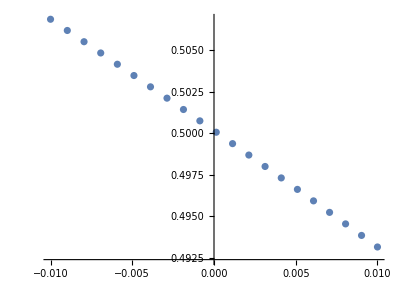

```mathematica
ComplexListPlot[Table[pplus[%90[[2]],z,0.5^2],{z,-1,1,0.1}]]
```